```mathematica
(* https://github.com/shahin-mansouri *)
(* Ravesh seri tavani *)
(* martabe 2 *)
(* Inputs *)
f[x_, y_]= (1 + 2y)/x;
Subscript[x, 0] = 1; Subscript[y, 0] = 0;
xStop = 1.4;
iter = 20;
```

```mathematica
(* Funciton *)
seritavaniMethod[func_, a_, b_, xStop_, iter_]:=(
x[0] = a; y[0] = b;
h = (xStop - x[0])/iter;
fx[x_, y_] = D[func[x, y], x];
fy[x_, y_] = D[func[x, y], y];

Do[
y[n+1] = y[n] + h f[x[n], y[n]] + h^2/2(fx[x[n], y[n]]+fy[x[n], y[n]]*f[x[n], y[n]]);
x[n + 1] = x[n] + h;
(* Print[x[n]," -> ",  y[n]]; *)
, {n, 0, iter}];

Return[Table[{x[i], y[i]}, {i, 0, iter}]]
);
```

```mathematica
(* Output *)
answer = seritavaniMethod[f, Subscript[x, 0], Subscript[y, 0], xStop, iter]
```

{{1,0},{1.02,0.0202},{1.04,0.0408},{1.06,0.0618},{1.08,0.0832},{1.1,0.105},{1.12,0.1272},{1.14,0.1498},{1.16,0.1728},{1.18,0.1962},{1.2,0.22},{1.22,0.2442},{1.24,0.2688},{1.26,0.2938},{1.28,0.3192},{1.3,0.345},{1.32,0.3712},{1.34,0.3978},{1.36,0.4248},{1.38,0.4522},{1.4,0.48}}

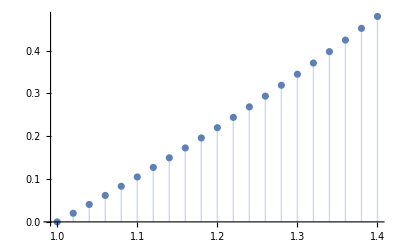

```mathematica
p2 = ListPlot[answer, Filling->Axis]
```

```mathematica
(*solution = DSolve[y'[x] == (1+2y[x])/x, y[x], x];
g[x_] = y[x]/.solution[[1]];
t[x_] = Table[g[x]/.C[1]->j, {j, 1, 1.4}];
p1 = Plot[t[x], {x, 1, 1.4}];
(*p2 = ListPlot[answer, Filling->Axis];*)
(* Show[p1, p2] *)
Show[p1, p2]*)
```